### Define the function that convert numbers to the format in file names

```mathematica
number2Printed[number_]:=Module[{returnedString="e",foo,bar,idx,oom},If[number==1,Return["1.0e+00"],If[number==0,Return["0.0e+00"],
If[number<1,
For[idx=1,StringLength[returnedString]==1,idx=idx+1,
foo=Floor[number/10^(-idx)];
If[foo==0,,
bar=Round[(number-foo*10^(-idx))/10^(-idx-1)];
If[StringLength[ToString[idx]]==1,
returnedString=StringJoin[ToString[foo],".",ToString[bar],returnedString,"-0",ToString[idx]],
returnedString=StringJoin[ToString[foo],".",ToString[bar],returnedString,"-",ToString[idx]]
]
]
];
Return[returnedString]
,
oom=(StringLength[ToString[DecimalForm[Floor[number]*1.]]]-2);
foo=Floor[number/10^oom];
bar=Round[(number-foo*10^oom)/10^(oom-1)];
If[StringLength[ToString[oom]]==1,
returnedString=StringJoin[ToString[foo],".",ToString[bar],returnedString,"+0",ToString[oom]],
returnedString=StringJoin[ToString[foo],".",ToString[bar],returnedString,"+",ToString[oom]]
];
Return[returnedString]
];
]
]
]
```

### Import parameters

```mathematica
combinedParameters= Interpreter[DelimitedSequence["Number",{"[",", ","]"}]][Import[StringJoin[NotebookDirectory[],"combined_parameters.txt"]]];
sequenceLengths= Interpreter[DelimitedSequence["Number",{"[",", ","]"}]][Import[StringJoin[NotebookDirectory[],"sequence_lengths.txt"]]];
populationSizes= Interpreter[DelimitedSequence["Number",{"[",", ","]"}]][Import[StringJoin[NotebookDirectory[],"population_sizes.txt"]]];
```

### Import data

```mathematica
histograms=Table[Table[Table[Transpose[
Interpreter[DelimitedSequence[DelimitedSequence["Number",{"[",", ","]"}],{"[",", ","]"}]][Import[StringJoin[NotebookDirectory[],number2Printed[combinedParameters[[idx1]]],"_",number2Printed[sequenceLengths[[idx2]]],"_",number2Printed[populationSizes[[idx3]]],".txt"]]]
],{idx3,Length[populationSizes]}],{idx2,Length[sequenceLengths]}],{idx1,Length[combinedParameters]}];
```

### Plot the data and the prediction

```mathematica
prediction[tau_,combinedParameter_]:=(combinedParameter*tau+1)*Exp[-combinedParameter*tau^2/2-tau];
```

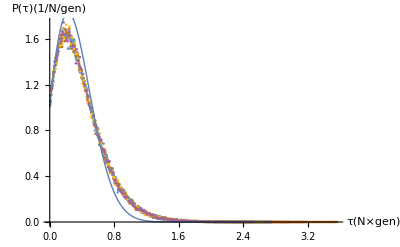

```mathematica
With[{idx0=6},Show[ListPlot[Flatten[Table[Table[histograms[[idx0,idx1,idx2]],{idx2,Length[populationSizes]}],{idx1,Length[sequenceLengths]}],1],ImageSize->Full,PlotRange->All,AxesLabel->{"τ(N×gen)","P(τ)(1/N/gen)"}],Plot[prediction[tau,combinedParameters[[idx0]]],{tau,0,Transpose[Max[histograms[[idx0,1,1]]]][[1]]},PlotStyle->Thick]]]
```

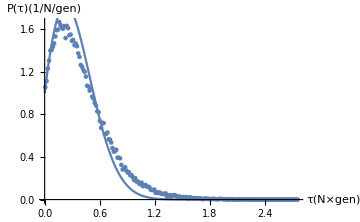
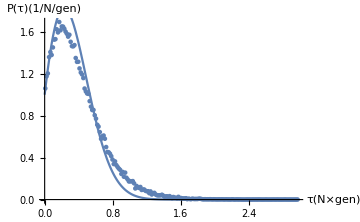
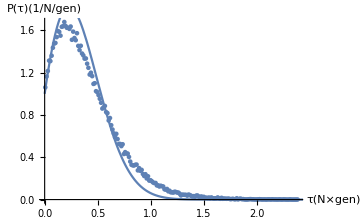
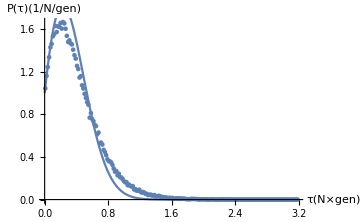
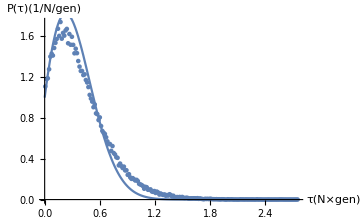
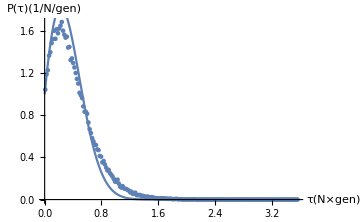
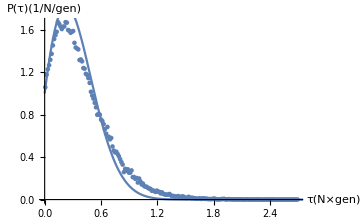
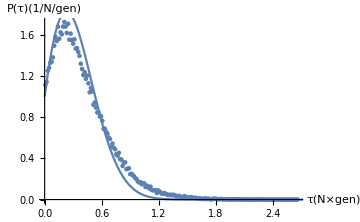

```mathematica
With[{idx0=6},Table[Table[
Show[ListPlot[histograms[[idx0,idx1,idx2]],ImageSize->Medium,PlotRange->All,AxesLabel->{"τ(N×gen)","P(τ)(1/N/gen)"}],Plot[(combinedParameters[[idx0]]*tau+1)Exp[-combinedParameters[[idx0]]/2*tau^2-tau],{tau,0,Transpose[Max[histograms[[idx0,1,1]]]][[1]]},PlotRange->All]],
{idx2,Length[populationSizes]}],{idx1,Length[sequenceLengths]}]]
```

### Plot the errors

```mathematica
errors=Table[Flatten[Table[Table[histograms[[idx0,idx1,idx2]],{idx2,Length[populationSizes]}],{idx1,Length[sequenceLengths]}],2],{idx0,Length[combinedParameters]}];
Do[Do[errors[[idx0,idx1]]={errors[[idx0,idx1,1]],errors[[idx0,idx1,2]]-prediction[errors[[idx0,idx1,1]],combinedParameters[[idx0]]]},{idx1,Length[errors[[idx0]]]}],{idx0,Length[combinedParameters]}]
```

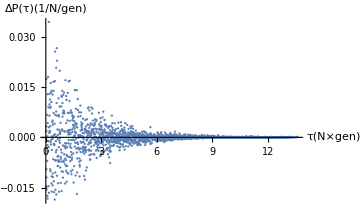
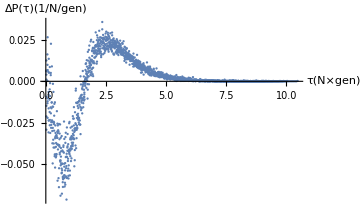
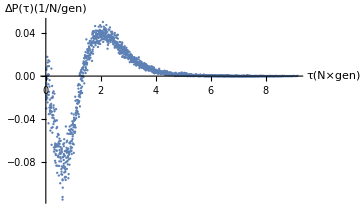
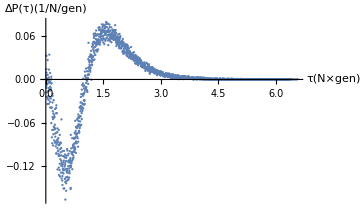
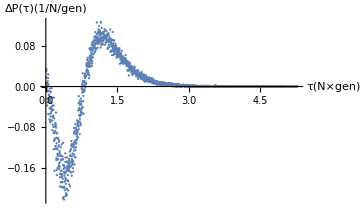
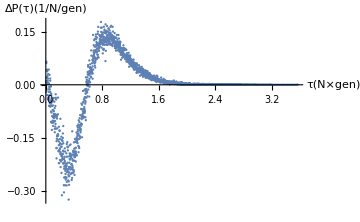
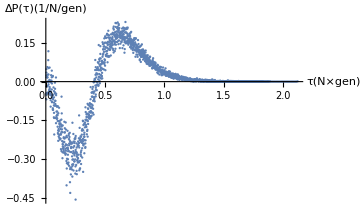
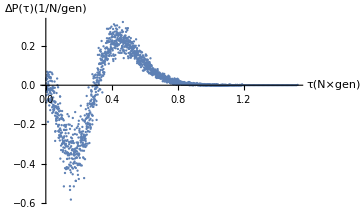

```mathematica
Table[Table[
ListPlot[errors[[3*(idx1-1)+idx2]],ImageSize->Medium,PlotRange->All,AxesLabel->{"τ(N×gen)","ΔP(τ)(1/N/gen)"}],{idx2,3}],{idx1,Ceiling[Length[combinedParameters]/3]}]
```

### Fit scaling factors

```mathematica
predictionFree[tau_,gamma_,beta_,alpha_,combinedParameter_]:=(3gamma*tau^2+beta*combinedParameter*tau+alpha)*Exp[-gamma*tau^3-beta*combinedParameter*tau^2/2-alpha*tau]
```

```mathematica
gammas=Table[0,{idx,Length[combinedParameters]}];
betas=Table[0,{idx,Length[combinedParameters]}];
alphas=Table[0,{idx,Length[combinedParameters]}];
Module[{fit=Table[0,{idx0,Length[combinedParameters]}]},Do[
fit[[idx0]]=NonlinearModelFit[
Flatten[Table[Table[histograms[[idx0,idx1,idx2]],{idx2,Length[populationSizes]}],{idx1,Length[sequenceLengths]}],2],
predictionFree[tau,gamma,beta,alpha,combinedParameters[[idx0]]],{gamma,beta,alpha},tau];
gammas[[idx0]]=fit[[idx0]]["ParameterTable"][[1,1,2,2]];
betas[[idx0]]=fit[[idx0]]["ParameterTable"][[1,1,3,2]];
alphas[[idx0]]=fit[[idx0]]["ParameterTable"][[1,1,4,2]],
{idx0,Length[combinedParameters]}]]
```

General::munfl: Exp[-6525.05] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

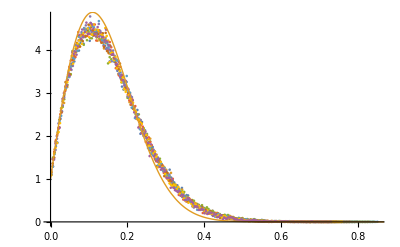

```mathematica
With[{idx0=12},Show[ListPlot[Flatten[Table[Table[histograms[[idx0,idx1,idx2]],{idx2,Length[populationSizes]}],{idx1,Length[sequenceLengths]}],1],ImageSize->Full,PlotRange->All],Plot[{predictionFree[tau,gammas[[idx0]],betas[[idx0]],alphas[[idx0]],combinedParameters[[idx0]]],predictionFree[tau,0,1,1,combinedParameters[[idx0]]]},{tau,0,Transpose[Max[histograms[[idx0,1,1]]]][[1]]},PlotRange->All,PlotStyle->Thick,AxesLabel->{"τ(N×gen)","P(τ)(1/N/gen)"}]]]
```

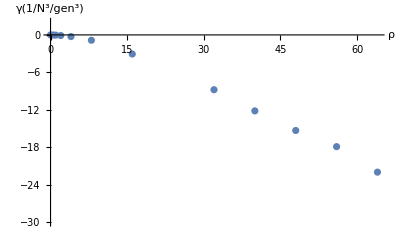

```mathematica
ListPlot[Transpose[{combinedParameters,gammas}],PlotRange->{-30,2},AxesLabel->{"ρ","γ(1/N^3/gen^3)"}]
```

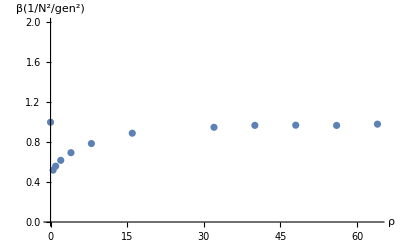

```mathematica
ListPlot[Transpose[{combinedParameters,betas}],PlotRange->{0,2},AxesLabel->{"ρ","β(1/N^2/gen^2)"}]
```

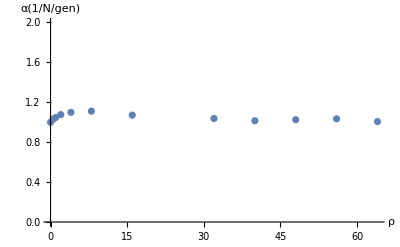

```mathematica
ListPlot[Transpose[{combinedParameters,alphas}],PlotRange->{0,2},AxesLabel->{"ρ","α(1/N/gen)"}]
```